# FOR PLOTTING

```mathematica
SetDirectory[NotebookDirectory[]];

NrFrames=174;
Lx=10;Ly=10;

For[idk=1,idk<=NrFrames,idk++,
BasalSidesx=Import["./output/X_"<>ToString[idk]<>".txt","Table"];
BasalSidesy=Import["./output/Y_"<>ToString[idk]<>".txt","Table"];
BasalSidesxS=Import["./output/XS_"<>ToString[idk]<>".txt","Table"];
BasalSidesyS=Import["./output/YS_"<>ToString[idk]<>".txt","Table"];

For[j=1,j<=Length[BasalSidesx],j++,
nrsides=Abs[BasalSidesx[[j,1]]];

Bpolygon1[j]={};Bpolygon2[j]={};Bpolygon3[j]={};Bpolygon4[j]={};Bpolygon5[j]={};Bpolygon6[j]={};Bpolygon7[j]={};Bpolygon8[j]={};Bpolygon9[j]={};

Bpolygon1S[j]={};Bpolygon2S[j]={};Bpolygon3S[j]={};Bpolygon4S[j]={};Bpolygon5S[j]={};Bpolygon6S[j]={};Bpolygon7S[j]={};Bpolygon8S[j]={};Bpolygon9S[j]={};

For[i=2,i≤1+nrsides,i++,
AppendTo[Bpolygon1[j],{BasalSidesx[[j,i]],BasalSidesy[[j,i]]}];
AppendTo[Bpolygon2[j],{BasalSidesx[[j,i]]+Lx,BasalSidesy[[j,i]]}];
AppendTo[Bpolygon3[j],{BasalSidesx[[j,i]]+Lx,BasalSidesy[[j,i]]+Ly}];
AppendTo[Bpolygon4[j],{BasalSidesx[[j,i]],BasalSidesy[[j,i]]+Ly}];
AppendTo[Bpolygon5[j],{BasalSidesx[[j,i]]-Lx,BasalSidesy[[j,i]]+Ly}];
AppendTo[Bpolygon6[j],{BasalSidesx[[j,i]]-Lx,BasalSidesy[[j,i]]}];
AppendTo[Bpolygon7[j],{BasalSidesx[[j,i]]-Lx,BasalSidesy[[j,i]]-Ly}];
AppendTo[Bpolygon8[j],{BasalSidesx[[j,i]],BasalSidesy[[j,i]]-Ly}];
AppendTo[Bpolygon9[j],{BasalSidesx[[j,i]]+Lx,BasalSidesy[[j,i]]-Ly}];
AppendTo[Bpolygon1S[j],{BasalSidesxS[[j,i]],BasalSidesyS[[j,i]]}];
AppendTo[Bpolygon2S[j],{BasalSidesxS[[j,i]]+Lx,BasalSidesyS[[j,i]]}];
AppendTo[Bpolygon3S[j],{BasalSidesxS[[j,i]]+Lx,BasalSidesyS[[j,i]]+Ly}];
AppendTo[Bpolygon4S[j],{BasalSidesxS[[j,i]],BasalSidesyS[[j,i]]+Ly}];
AppendTo[Bpolygon5S[j],{BasalSidesxS[[j,i]]-Lx,BasalSidesyS[[j,i]]+Ly}];
AppendTo[Bpolygon6S[j],{BasalSidesxS[[j,i]]-Lx,BasalSidesyS[[j,i]]}];
AppendTo[Bpolygon7S[j],{BasalSidesxS[[j,i]]-Lx,BasalSidesyS[[j,i]]-Ly}];
AppendTo[Bpolygon8S[j],{BasalSidesxS[[j,i]],BasalSidesyS[[j,i]]-Ly}];
AppendTo[Bpolygon9S[j],{BasalSidesxS[[j,i]]+Lx,BasalSidesyS[[j,i]]-Ly}];
];

Bpolygon1[j]=Polygon[Bpolygon1[j]];
Bpolygon2[j]=Polygon[Bpolygon2[j]];Bpolygon3[j]=Polygon[Bpolygon3[j]];Bpolygon4[j]=Polygon[Bpolygon4[j]];Bpolygon5[j]=Polygon[Bpolygon5[j]];Bpolygon6[j]=Polygon[Bpolygon6[j]];Bpolygon7[j]=Polygon[Bpolygon7[j]];Bpolygon8[j]=Polygon[Bpolygon8[j]];Bpolygon9[j]=Polygon[Bpolygon9[j]];

Bpolygon1S[j]=Polygon[Bpolygon1S[j]];
Bpolygon2S[j]=Polygon[Bpolygon2S[j]];Bpolygon3S[j]=Polygon[Bpolygon3S[j]];Bpolygon4S[j]=Polygon[Bpolygon4S[j]];Bpolygon5S[j]=Polygon[Bpolygon5S[j]];Bpolygon6S[j]=Polygon[Bpolygon6S[j]];Bpolygon7S[j]=Polygon[Bpolygon7S[j]];Bpolygon8S[j]=Polygon[Bpolygon8S[j]];Bpolygon9S[j]=Polygon[Bpolygon9S[j]];

];

edgThick=0.0025;

slikaB1=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon1[j]},{j,1,Length[BasalSidesx]}];
slikaB2=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon2[j]},{j,1,Length[BasalSidesx]}];
slikaB3=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon3[j]},{j,1,Length[BasalSidesx]}];
slikaB4=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon4[j]},{j,1,Length[BasalSidesx]}];
slikaB5=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon5[j]},{j,1,Length[BasalSidesx]}];
slikaB6=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon6[j]},{j,1,Length[BasalSidesx]}];
slikaB7=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon7[j]},{j,1,Length[BasalSidesx]}];
slikaB8=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon8[j]},{j,1,Length[BasalSidesx]}];
slikaB9=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],Gray,Bpolygon9[j]},{j,1,Length[BasalSidesx]}];

slikaB1S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[1],White,Bpolygon1S[j]},{j,1,Length[BasalSidesx]}];
slikaB2S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon2S[j]},{j,1,Length[BasalSidesx]}];
slikaB3S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon3S[j]},{j,1,Length[BasalSidesx]}];
slikaB4S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon4S[j]},{j,1,Length[BasalSidesx]}];
slikaB5S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon5S[j]},{j,1,Length[BasalSidesx]}];
slikaB6S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon6S[j]},{j,1,Length[BasalSidesx]}];
slikaB7S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon7S[j]},{j,1,Length[BasalSidesx]}];
slikaB8S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon8S[j]},{j,1,Length[BasalSidesx]}];
slikaB9S=Table[{EdgeForm[Directive[Thickness[edgThick],Black]],Opacity[0],Gray,Bpolygon9S[j]},{j,1,Length[BasalSidesx]}];

FramE[idk]=Show[
Graphics[
{
slikaB1S,slikaB2S,slikaB3S,slikaB4S,slikaB5S,slikaB6S,slikaB7S,slikaB8S,slikaB9S,
slikaB1,slikaB2,slikaB3,slikaB4,slikaB5,slikaB6,slikaB7,slikaB8,slikaB9
},
PlotRange->{{0,Lx},{0,Ly}},PlotRangeClipping->True,ImageSize->350
]
];

];
```

```mathematica
Manipulate[Show[
FramE[idk],
Plot[0.2(x-5)^2+4-Ly/3,{x,0,10}]
],{idk,1,NrFrames,1}]
```

# SHOULDER VERTEX-VERTEX

```mathematica
rvi={vix,viy};
rvj={vjx,vjy};
e=rvj-rvi;
d=Norm[e];
FullSimplify[kS(lS-d)^2]
```

kS (lS-√(Abs[vix-vjx]^2+Abs[viy-vjy]^2))^2

```mathematica
FullSimplify[-Grad[kS (lS-√((vix-vjx)^2+(viy-vjy)^2))^2,{vix,viy}]]
FullSimplify[-Grad[kS (lS-√((vix-vjx)^2+(viy-vjy)^2))^2,{vjx,vjy}]]
```

{(2 kS (vix-vjx) (lS-√((vix-vjx)^2+(viy-vjy)^2)))/(√((vix-vjx)^2+(viy-vjy)^2)),(2 kS (lS-√((vix-vjx)^2+(viy-vjy)^2)) (viy-vjy))/(√((vix-vjx)^2+(viy-vjy)^2))}

{(2 kS (vix-vjx) (-lS+√((vix-vjx)^2+(viy-vjy)^2)))/(√((vix-vjx)^2+(viy-vjy)^2)),(2 kS (-lS+√((vix-vjx)^2+(viy-vjy)^2)) (viy-vjy))/(√((vix-vjx)^2+(viy-vjy)^2))}

```mathematica
CForm[(2 kS (-lS+√((vix-vjx)^2+(viy-vjy)^2)) (viy-vjy))/(√((vix-vjx)^2+(viy-vjy)^2))]
```

(2*kS*(-lS + Sqrt(Power(vix - vjx,2) + Power(viy - vjy,2)))*
     (viy - vjy))/Sqrt(Power(vix - vjx,2) + Power(viy - vjy,2))

# STERIC REPULSION

```mathematica
rv1={v1x,v1y};
rv2={v2x,v2y};
e=rv2-rv1;
t=FullSimplify[e/Norm[e]];
n={t[[2]],-t[[1]]};
R={vx-v1x,vy-v1y};
FullSimplify[R.n]
FullSimplify[(R.n)^2]
```

(v1y (v2x-vx)+v2y vx-v2x vy+v1x (-v2y+vy))/(√(Abs[v1x-v2x]^2+Abs[v1y-v2y]^2))

(v1y v2x-v1x v2y-v1y vx+v2y vx+v1x vy-v2x vy)^2/(Abs[v1x-v2x]^2+Abs[v1y-v2y]^2)

```mathematica
FullSimplify[Grad[(v1y v2x-v1x v2y-v1y vx+v2y vx+v1x vy-v2x vy)^2/((v1x-v2x)^2+(v1y-v2y)^2),{v1x,v1y}]]
FullSimplify[Grad[(v1y v2x-v1x v2y-v1y vx+v2y vx+v1x vy-v2x vy)^2/((v1x-v2x)^2+(v1y-v2y)^2),{v2x,v2y}]]
FullSimplify[Grad[(v1y v2x-v1x v2y-v1y vx+v2y vx+v1x vy-v2x vy)^2/((v1x-v2x)^2+(v1y-v2y)^2),{vx,vy}]]
```

{(2 (v1y-v2y) ((v1x-v2x) (v2x-vx)+(v1y-v2y) (v2y-vy)) (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy))/((v1x-v2x)^2+(v1y-v2y)^2)^2,-((2 (v1x-v2x) ((v1x-v2x) (v2x-vx)+(v1y-v2y) (v2y-vy)) (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy))/((v1x-v2x)^2+(v1y-v2y)^2)^2)}

{(2 (v1y-v2y) (v1y (v2x-vx)+v2y vx-v2x vy+v1x (-v2y+vy)) (v1x^2+v1y^2+v2x vx-v1x (v2x+vx)+v2y vy-v1y (v2y+vy)))/((v1x-v2x)^2+(v1y-v2y)^2)^2,(2 (v1x-v2x) (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy) (v1x^2+v1y^2+v2x vx-v1x (v2x+vx)+v2y vy-v1y (v2y+vy)))/((v1x-v2x)^2+(v1y-v2y)^2)^2}

{(2 (-v1y+v2y) (v1y (v2x-vx)+v2y vx-v2x vy+v1x (-v2y+vy)))/((v1x-v2x)^2+(v1y-v2y)^2),(2 (v1x-v2x) (v1y (v2x-vx)+v2y vx-v2x vy+v1x (-v2y+vy)))/((v1x-v2x)^2+(v1y-v2y)^2)}

```mathematica
CForm[(2 (-v1y+v2y) (v1y (v2x-vx)+v2y vx-v2x vy+v1x (-v2y+vy)))/((v1x-v2x)^2+(v1y-v2y)^2)]
```

(2*(-v1y + v2y)*(v1y*(v2x - vx) + v2y*vx - v2x*vy + v1x*(-v2y + vy)))/
   (Power(v1x - v2x,2) + Power(v1y - v2y,2))

```mathematica
CForm[(2 (v1x-v2x) (v1y (v2x-vx)+v2y vx-v2x vy+v1x (-v2y+vy)))/((v1x-v2x)^2+(v1y-v2y)^2)]
```

(2*(v1x - v2x)*(v1y*(v2x - vx) + v2y*vx - v2x*vy + v1x*(-v2y + vy)))/
   (Power(v1x - v2x,2) + Power(v1y - v2y,2))

# SHOULDER

```mathematica
rv1={v1x,v1y};
rv2={v2x,v2y};
e=rv2-rv1;
t=FullSimplify[e/Norm[e]];
n={t[[2]],-t[[1]]};
R={vx-v1x,vy-v1y};
FullSimplify[R.n];
FullSimplify[kS(lS-R.n)^2]
```

(kS (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy+lS √(Abs[v1x-v2x]^2+Abs[v1y-v2y]^2))^2)/(Abs[v1x-v2x]^2+Abs[v1y-v2y]^2)

```mathematica
(kS (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy+lS √((v1x-v2x)^2+(v1y-v2y)^2))^2)/((v1x-v2x)^2+(v1y-v2y)^2)
```

```mathematica
FullSimplify[Grad[(kS (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy+lS √((v1x-v2x)^2+(v1y-v2y)^2))^2)/((v1x-v2x)^2+(v1y-v2y)^2),{v1x,v1y}]]
FullSimplify[Grad[(kS (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy+lS √((v1x-v2x)^2+(v1y-v2y)^2))^2)/((v1x-v2x)^2+(v1y-v2y)^2),{v2x,v2y}]]
FullSimplify[Grad[(kS (-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy+lS √((v1x-v2x)^2+(v1y-v2y)^2))^2)/((v1x-v2x)^2+(v1y-v2y)^2),{vx,vy}]]
```

{1/(((v1x-v2x)^2+(v1y-v2y)^2)^2)2 kS (v1y-v2y) ((v1x-v2x) (v2x-vx)+(v1y-v2y) (v2y-vy)) (lS √((v1x-v2x)^2+(v1y-v2y)^2)-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy),-1/(((v1x-v2x)^2+(v1y-v2y)^2)^2)2 kS (v1x-v2x) ((v1x-v2x) (v2x-vx)+(v1y-v2y) (v2y-vy)) (lS √((v1x-v2x)^2+(v1y-v2y)^2)-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy)}

{-1/(((v1x-v2x)^2+(v1y-v2y)^2)^2)2 kS (v1y-v2y) (lS √((v1x-v2x)^2+(v1y-v2y)^2)-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy) (v1x^2+v1y^2+v2x vx-v1x (v2x+vx)+v2y vy-v1y (v2y+vy)),1/(((v1x-v2x)^2+(v1y-v2y)^2)^2)2 kS (v1x-v2x) (lS √((v1x-v2x)^2+(v1y-v2y)^2)-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy) (v1x^2+v1y^2+v2x vx-v1x (v2x+vx)+v2y vy-v1y (v2y+vy))}

{(2 kS (v1y-v2y) (lS √((v1x-v2x)^2+(v1y-v2y)^2)-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy))/((v1x-v2x)^2+(v1y-v2y)^2),(2 kS (-v1x+v2x) (lS √((v1x-v2x)^2+(v1y-v2y)^2)-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy))/((v1x-v2x)^2+(v1y-v2y)^2)}

```mathematica
CForm[(2 kS (-v1x+v2x) (lS √((v1x-v2x)^2+(v1y-v2y)^2)-v2y vx+v1y (-v2x+vx)+v1x (v2y-vy)+v2x vy))/((v1x-v2x)^2+(v1y-v2y)^2)]
```

(2*kS*(-v1x + v2x)*(lS*Sqrt(Power(v1x - v2x,2) + Power(v1y - v2y,2)) - v2y*vx + v1y*(-v2x + vx) + v1x*(v2y - vy) + v2x*vy))/
   (Power(v1x - v2x,2) + Power(v1y - v2y,2))

# CELL STABILITY

```mathematica
FullSimplify[Solve[a^3-2a^2+a-c==0,a]]
```

{{a→1/3 (2+1/(-1+(27 c)/2+3/2 √3 √(c (-4+27 c)))^(1/3)+(-1+(27 c)/2+3/2 √3 √(c (-4+27 c)))^(1/3))},{a→1/6 (4-(2 (-2)^(1/3))/(-2+27 c+3 √3 √(c (-4+27 c)))^(1/3)+(-2)^(2/3) (-2+27 c+3 √3 √(c (-4+27 c)))^(1/3))},{a→1/6 (4+(2 (-1)^(2/3))/(-1+(27 c)/2+3/2 √3 √(c (-4+27 c)))^(1/3)+(-2+27 c+3 √3 √(c (-4+27 c)))^(1/3) Root-0.794-1.37 ⅈRoot[-4+#1^3&,2]-0.7937005259840998)}}

```mathematica
sol[c_]:=1/3 (2+1/(-1+(27 c)/2+3/2 √3 √(c (-4+27 c)))^(1/3)+(-1+(27 c)/2+3/2 √3 √(c (-4+27 c)))^(1/3));
```

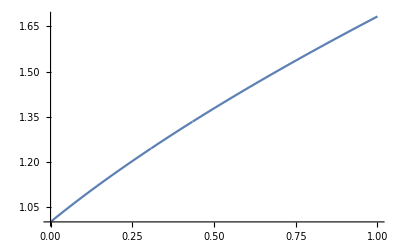

```mathematica
Plot[
sol[γ^2π/4],{γ,0,1}
]
```

```mathematica
Manipulate[
Plot[-2(a-1)-γ Sqrt[π] a^(-1/2),{a,0,2}],
{γ,0,1}
]
```

```mathematica
sol=Assuming[{a>0,γ>0},FullSimplify[Solve[0==-2(a-1)-γ Sqrt[π] a^(-1/2),a]]]
```

{{a→ConditionalExpression[Root[-π γ^2+4 #1-8 #1^2+4 #1^3&,1], γ<4/(3 √(3 π))]},{a→ConditionalExpression[Root[-π γ^2+4 #1-8 #1^2+4 #1^3&,2], γ<4/(3 √(3 π))]}}

```mathematica
a/.sol[[1]]
```

ConditionalExpression[Root[-π γ^2+4 #1-8 #1^2+4 #1^3&,1], γ<4/(3 √(3 π))]

```mathematica
4./(3 √(3 π))
```

0.434313

# SOFT SHOULDER (simplified)

```mathematica
r[i_]:={x[i],y[i]};
e[i_]:={(x[i]-x[i-1])/l[i],(y[i]-y[i-1])/l[i]};
n[i_]:={(y[i]-y[i-1])/l[i],-(x[i]-x[i-1])/l[i]};
```

```mathematica
(*d[i]=n[i]+n[i+1];FullSimplify[d[i]/Sqrt[d[i][[1]]^2+d[i][[2]]^2]]*)
d[i_]:={(l[1+i](-y[-1+i]+y[i])+l[i](-y[i]+y[1+i]))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)),(l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2))}
```

```mathematica
FullSimplify[{x[i],y[i]}+Ls*d[i]]
```

{x[i]+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)),y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2))}

```mathematica
(*rS[i_]:={x[i],y[i]}+Ls*d[i]*)
rS[i_]:={x[i]+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)),y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2))}
```

```mathematica
FullSimplify[rS[i]-rS[i-1]]
```

{-x[-1+i]+x[i]+(Ls (l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)),-y[-1+i]+(Ls (l[i] (-x[-2+i]+x[-1+i])+l[-1+i] (-x[-1+i]+x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2))}

```mathematica
rS[i]-rS[i-1]
```

{-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)),-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2))}

```mathematica
(*rS[i]-rS[i-1]*)
eS[i_]:={-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)),-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2))}
```

```mathematica
eS[i]/Sqrt[eS[i][[1]]^2+eS[i][[2]]^2]
```

{(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))/(√((-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2+(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2)),(-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))/(√((-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2+(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2))}

```mathematica
(*eS[i]/Sqrt[eS[i][[1]]^2+eS[i][[2]]^2]*)
eS[i_]:={(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))/(√((-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2+(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2)),(-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))/(√((-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2+(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2))}
```

```mathematica
(*nS[i]={eS[i][[2]],-eS[i][[1]]}*)
nS[i_]:={(-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))/(√((-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2+(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2)),-((-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))/(√((-y[-1+i]-(Ls (l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+y[i]+(Ls (l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2+(-x[-1+i]+x[i]-(Ls (l[i] (-y[-2+i]+y[-1+i])+l[-1+i] (-y[-1+i]+y[i])))/(√((l[i] (x[-2+i]-x[-1+i])+l[-1+i] (x[-1+i]-x[i]))^2+(l[i] (y[-2+i]-y[-1+i])+l[-1+i] (y[-1+i]-y[i]))^2))+(Ls (l[1+i] (-y[-1+i]+y[i])+l[i] (-y[i]+y[1+i])))/(√((l[1+i] (x[-1+i]-x[i])+l[i] (x[i]-x[1+i]))^2+(l[1+i] (y[-1+i]-y[i])+l[i] (y[i]-y[1+i]))^2)))^2)))}
```

```mathematica
l[i_]:=√((x[i]-x[i-1])^2+(y[i]-y[i-1])^2);
```

```mathematica
CForm[-Grad[((r[j]-rS[i-1]).nS[i])^2,{x[j],y[j]}][[1]]]
```

(-2*(-y(-1 + i) + y(i) - (Ls*((x(-1 + i) - x(i))*
             Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
            (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
        Sqrt(Power((x(-1 + i) - x(i))*Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
               Power(-y(-2 + i) + y(-1 + i),2)) + 
            (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2) + 
          Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
             (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
             Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
       (Ls*((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
            (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
        Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
            (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
          Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
            (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)))*
     (((-x(-1 + i) + x(j) - (Ls*(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (-y(-1 + i) + y(i)) + (-y(-2 + i) + y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)))*
          (-y(-1 + i) + y(i) - (Ls*((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
            (Ls*((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
             Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
               Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
                 (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2))))/
        Sqrt(Power(-y(-1 + i) + y(i) - (Ls*
               ((x(-1 + i) - x(i))*Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
                    Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
            (Ls*((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
             Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
               Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
                 (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)),2) + 
          Power(-x(-1 + i) + x(i) - (Ls*(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
                    Power(-y(-2 + i) + y(-1 + i),2))*(-y(-1 + i) + y(i)) + 
                 (-y(-2 + i) + y(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
            (Ls*(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(-y(i) + y(1 + i)) + 
                 (-y(-1 + i) + y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
             Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
               Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
                 (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)),2)) - 
       ((-x(-1 + i) + x(i) - (Ls*(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (-y(-1 + i) + y(i)) + (-y(-2 + i) + y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
            (Ls*(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(-y(i) + y(1 + i)) + 
                 (-y(-1 + i) + y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
             Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
               Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
                 (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)))*
          (-y(-1 + i) - (Ls*((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + y(j)))/
        Sqrt(Power(-y(-1 + i) + y(i) - (Ls*
               ((x(-1 + i) - x(i))*Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
                    Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
            (Ls*((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
             Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
               Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
                 (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)),2) + 
          Power(-x(-1 + i) + x(i) - (Ls*(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
                    Power(-y(-2 + i) + y(-1 + i),2))*(-y(-1 + i) + y(i)) + 
                 (-y(-2 + i) + y(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
             Sqrt(Power((x(-1 + i) - x(i))*
                  Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
                 (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)\
                + Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
                  (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
                  Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
            (Ls*(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(-y(i) + y(1 + i)) + 
                 (-y(-1 + i) + y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
             Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
                 (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
               Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
                 (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)),2))))/
   Sqrt(Power(-y(-1 + i) + y(i) - (Ls*((x(-1 + i) - x(i))*
             Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2)) + 
            (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
        Sqrt(Power((x(-1 + i) - x(i))*Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
               Power(-y(-2 + i) + y(-1 + i),2)) + 
            (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2) + 
          Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
             (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
             Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
       (Ls*((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
            (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
        Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
            (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
          Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
            (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)),2) + 
     Power(-x(-1 + i) + x(i) - (Ls*(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
               Power(-y(-2 + i) + y(-1 + i),2))*(-y(-1 + i) + y(i)) + 
            (-y(-2 + i) + y(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))))/
        Sqrt(Power((x(-1 + i) - x(i))*Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + 
               Power(-y(-2 + i) + y(-1 + i),2)) + 
            (x(-2 + i) - x(-1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2) + 
          Power(Sqrt(Power(-x(-2 + i) + x(-1 + i),2) + Power(-y(-2 + i) + y(-1 + i),2))*
             (y(-1 + i) - y(i)) + (y(-2 + i) - y(-1 + i))*
             Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)),2)) + 
       (Ls*(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(-y(i) + y(1 + i)) + 
            (-y(-1 + i) + y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2))))/
        Sqrt(Power((x(i) - x(1 + i))*Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2)) + 
            (x(-1 + i) - x(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2) + 
          Power(Sqrt(Power(-x(-1 + i) + x(i),2) + Power(-y(-1 + i) + y(i),2))*(y(i) - y(1 + i)) + 
            (y(-1 + i) - y(i))*Sqrt(Power(-x(i) + x(1 + i),2) + Power(-y(i) + y(1 + i),2)),2)),2))